# Dragon Kings

## Initialization and options

In order to execute this notebook and run a test of symmetry it is neccesary to first compile the TnSymmetryStatistic package.

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];
```

```mathematica
Middle[l_List]:=Part[l,Floor[Length[l]/2]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};

(* Opciones de los procedimientos *)
windowsize = 252;
skip = 20;
resolution = 40;
symmetryPoints = 50;
```

### Package information

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Load database

```mathematica
database = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","DJI_DAX_MXX_NIKKEI_dataset.mx"}]];
AddToDataset[database,"TrendReturns",TrendReturns,{"Prices"}];
AddToDataset[database,"DatedTrendReturns",DatedTrendReturns,{"Dates","Prices"}];
AddToDataset[database,"VelocityTrendReturns",VelocityTrendReturns,{"Prices"}];
AddToDataset[database,"DatedVelocityTrendReturns",DatedVelocityTrendReturns,{"Dates","Prices"}];
```

## Crisis dates

```mathematica
rules = {"Japanese asset\nprice bubble"-> "(a)","Tequila effect"->"(b)","Dotcom bubble"->"(c)","Subprime crisis"->"(d)","Brexit"->"(e)"};
dateNames = {"Japanese asset\nprice bubble","Tequila effect","Dotcom bubble","Subprime crisis","Brexit"}/.rules;
dateObjects = {DateObject[{1990,1,1},"Day","Gregorian",-5.],DateObject[{1994,1,1},"Day","Gregorian",-5.],DateObject[{2000,3,10},"Day","Gregorian",-5.],DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2016,6,23},"Day","Gregorian",-5.]};

AddKeyToMarket[database[[1]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[1]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[2]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[2]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[3]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[3]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[4]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[4]],"ImportantDates"->dateObjects];

orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
```

## Detección de fechas importantes

```mathematica
extremeDates = ProgressMap[GetExtremeEventDates[#["DatedTrendReturns"]]&,database]
```

{{Day: Thu 8 Oct 1998,Day: Wed 12 Mar 2003,Day: Tue 4 Sep 2001,Day: Wed 11 Sep 2002,Day: Mon 14 Jan 2008,Day: Fri 3 Oct 2008,Day: Tue 26 Jul 2011},{Day: Wed 9 Oct 2002,Day: Tue 11 Mar 2003,Day: Thu 20 Nov 2008,Day: Fri 14 Sep 2001,Day: Tue 30 Sep 2008},{Day: Thu 10 Sep 1998,Day: Mon 27 Oct 2008,Day: Fri 12 Jun 1992,Day: Tue 21 Jul 1992,Day: Wed 12 Aug 1992,Day: Thu 14 Apr 1994,Day: Wed 7 Dec 1994,Day: Thu 5 Jan 1995,Day: Wed 22 Feb 1995,Day: Tue 21 Oct 1997,Day: Tue 4 Nov 1997,Day: Wed 31 Dec 1997,Day: Fri 5 Jun 1998,Day: Thu 30 Jul 1998,Day: Tue 18 Aug 1998,Day: Tue 8 Sep 1998,Day: Wed 30 Dec 1998,Day: Mon 27 Mar 2000,Day: Fri 7 Apr 2000,Day: Tue 16 May 2000,Day: Fri 14 Jul 2000,Day: Mon 10 Sep 2001,Day: Fri 2 Jun 2006,Day: Wed 1 Oct 2008,Day: Mon 20 Oct 2008,Day: Fri 2 Jan 2009},{Day: Mon 17 Aug 1992,Day: Sun 26 Oct 2008,Day: Tue 30 Sep 2008,Day: Mon 20 Oct 2008}}

```mathematica
importantDates = FindImportantDates[extremeDates,3]
```

{Day: Fri 7 Sep 2001,Day: Wed 1 Oct 2008}

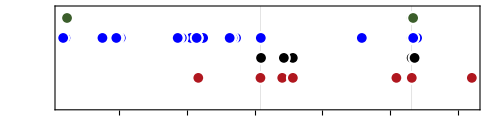

```mathematica
TimelinePlot[extremeDates,
PlotLegends->database[[All,"Name"]],
GridLines->{importantDates,None},
PlotTheme->"Monochrome",
PlotStyle->colors,
FrameLabel->{Style["Date",bigFontSize]}, 
ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
PlotMarkers->None,
Frame->True
]
```

```mathematica
importantDates = {DateObject[{2001,9,7},"Day","Gregorian",-5.],DateObject[{2008,10,1},"Day","Gregorian",-5.]};
```

```mathematica
importantDatesNames = {"DotCom Crisis","2008 Crisis"};
```

## Returns distribution

Figures 2-(b), 2-(c) and 2-(d).

```mathematica
MakeStatisticTable[marketnames_,dists_] := Module[{gridmm},
gridmm = {Join[{""},marketnames],
Join[{"μ"},Table[Mean[i],{i,dists}]],
Join[{"σ"}, Table[StandardDeviation[i],{i,dists}]],
Join[{"Skewness"}, Table[Skewness[i],{i,dists}]],
Join[{"Kurtosis"}, Table[Kurtosis[i],{i,dists}]]};
Grid[gridmm,
Alignment->Left,
Spacings->{2,1},
Frame->All,
ItemStyle->"Text",
Background->{{LightGray,None},{Gray,None}}
]
];
```

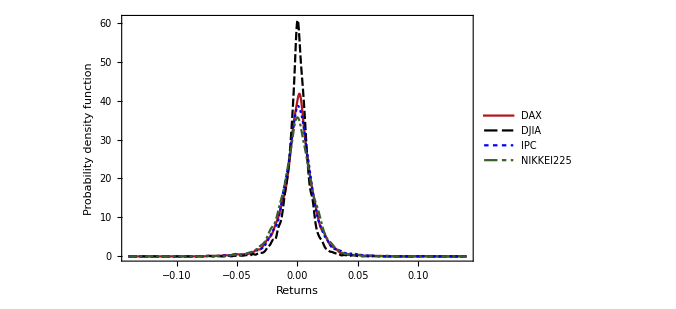

```mathematica
SmoothHistogram[database[[All,"Returns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["Returns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"Returns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000319714 | 0.000296114 | 0.000555369 | -0.0000312847
σ | 0.0142415 | 0.0107171 | 0.0148833 | 0.0151916
Skewness | -0.106661 | -0.176113 | 0.0226418 | -0.203261
Kurtosis | 7.30022 | 11.569 | 9.35525 | 8.09446

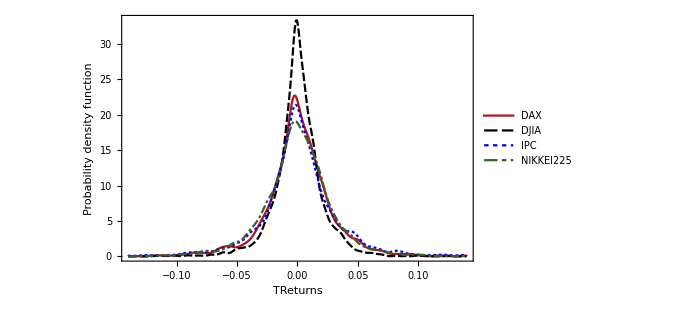

```mathematica
SmoothHistogram[database[[All,"TrendReturns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["TReturns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"TrendReturns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000631323 | 0.000563473 | 0.00120697 | -0.000059991
σ | 0.0295203 | 0.0208431 | 0.0342922 | 0.0300463
Skewness | -0.729049 | -0.693697 | -0.241625 | -0.569394
Kurtosis | 10.8335 | 14.9535 | 9.67833 | 11.9555

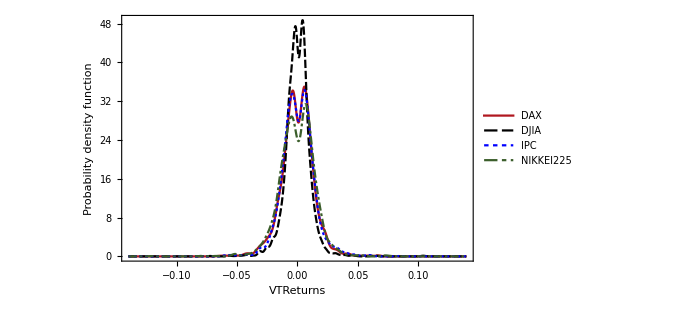

```mathematica
SmoothHistogram[database[[All,"VelocityTrendReturns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["VTReturns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"VelocityTrendReturns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000127415 | 0.000166781 | 0.00046062 | -0.0000621582
σ | 0.0131252 | 0.0103054 | 0.0131251 | 0.0142704
Skewness | -0.0275892 | 0.378788 | 0.152915 | -0.257632
Kurtosis | 5.43131 | 13.9691 | 5.84517 | 6.8131

```mathematica
hr = Map[{#["Name"],MeasureHeightRatio[#["VelocityTrendReturns"]]}&,database];
```

```mathematica
Grid[Prepend[hr,{"Name","Height ratio"}],Frame->All,Background->{None,{LightGray}}]
```

Name | Height ratio
DAX | 1.0235
DJIA | 1.02463
IPC | 1.02328
NIKKEI225 | 1.08783

## Cálculo de puntos de corte

```mathematica
Clear[HistogramPointPlot]
```

```mathematica
market = First[database];
```

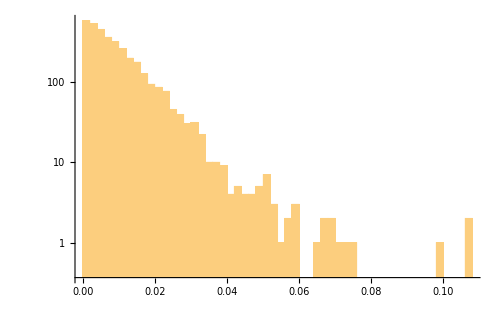

```mathematica
Histogram[Select[market["Returns"],Positive],PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
tbl = Table[{γ, PowerLawAndersonDarling[market["Returns"], γ]}, {γ, 0.01,0.030, 0.001}];
```

```mathematica
First@Last@MinimalBy[tbl,Last]
```

0.028

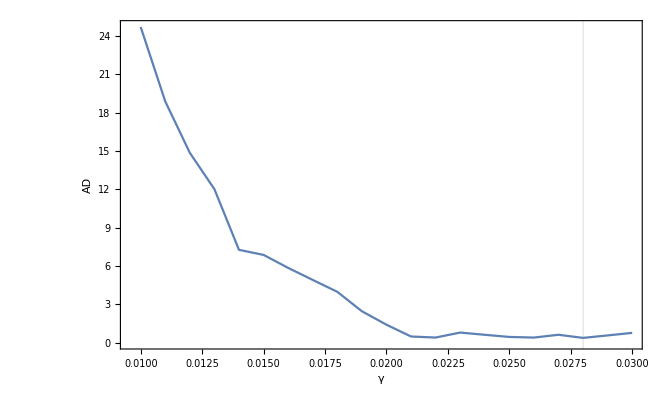

```mathematica
ListLinePlot[
tbl,
PlotRange->All,
Frame->True,
FrameLabel->{"γ","AD"},
GridLines->{{First@Last@MinimalBy[tbl,Last]},{}}
]
```

```mathematica
left = LeftCutoff[market["Returns"],0.01,0.030,0.001]
```

0.028

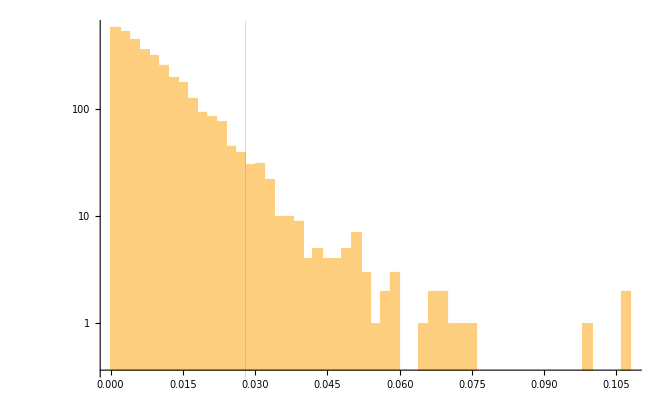

```mathematica
Histogram[Select[market["Returns"],Positive],GridLines->{{left},{}},ScalingFunctions->"Log",PlotRange->All]
```

```mathematica
right = RightCutoff[market["Returns"],left,0.15,0.001]
```

0.076

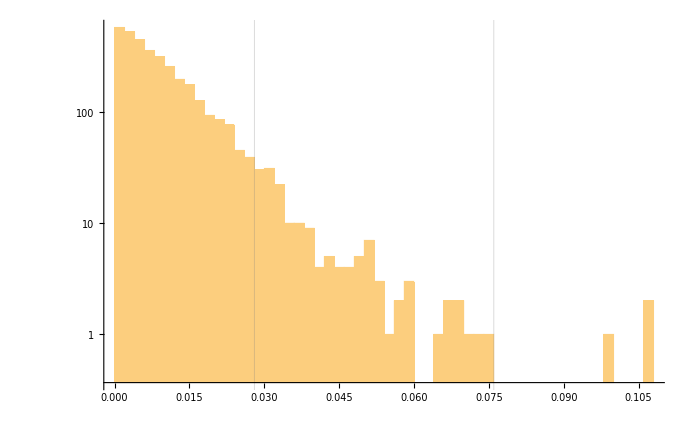

```mathematica
Histogram[Select[market["Returns"],Positive],GridLines->{{left,right},{}},ScalingFunctions->"Log",PlotRange->All]
```